```mathematica
(* MA39110 / Assignment 4.1 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=Pi;h=(xf-x0)/n;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
B=Table[0,{x,1,n-1}];
eps=0.0000000000001;
(*Initial Approximation: Parabola passing through the points (0,1/2),(1/2,0) and (Pi,-1/2).*)
f[x_]=(*(xf-x)y0/(xf-x0)+(x-x0)yf/(xf-x0)*)((Pi-1)/(Pi^2-Pi/2))x^2-((Pi^2-1/2)/(Pi^2-Pi/2))x+1/2;
YT=N[f[XT]];
While[{
Y=YT;
For[i=1,i<n,i++,
{
im=i+1;
A[[i,i]]=-2/h^2-2Y[[im]]+1;
If[i≠1,A[[i,i-1]]=1/h^2+(2/(4h^2))(Y[[im+1]]-Y[[im-1]])];
If[i≠n-1,A[[i,i+1]]=1/h^2-(2/(4h^2))(Y[[im+1]]-Y[[im-1]])];
B[[i]]=-(1/h^2)(Y[[im-1]]-2Y[[im]]+Y[[im+1]])+(1/(4h^2))(Y[[im+1]]-Y[[im-1]])^2+Y[[im]]^2-Y[[im]]-1;
}];
YT=Y+Flatten[{{0},Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B],{0}}];
};N[Max[Abs[YT-Y]]]>eps];
YT
];
```

```mathematica
in={50,100 ,200};
sol=Model[in[[1]]];
(*Print[N[sol]];*)
solt=NDSolve[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[x],x];
err1=Abs[NDSolveValue[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[XT],x]-sol];
perr1=ListPlot[Transpose[{XT,err1}],PlotStyle->Red];
Print[N[Max[err1]]];
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[((Pi-1)/(Pi^2-Pi/2))x^2-((Pi^2-1/2)/(Pi^2-Pi/2))x+1/2,{x,0,Pi},PlotStyle->{Dashed,Black}]}];
```

0.000474216

```mathematica
sol=Model[in[[2]]];
(*Print[N[sol]];*)
solt=NDSolve[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[x],x];
err2=Abs[NDSolveValue[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[XT],x]-sol];
perr2=ListPlot[Transpose[{XT,err2}],PlotStyle->Green];
Print[N[Max[err2]]];
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[((Pi-1)/(Pi^2-Pi/2))x^2-((Pi^2-1/2)/(Pi^2-Pi/2))x+1/2,{x,0,Pi},PlotStyle->{Dashed,Black}]}];
```

0.000118608

```mathematica
sol=Model[in[[3]]];
(*Print[N[sol]];*)
solt=NDSolve[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[x],x];
err3=Abs[NDSolveValue[{y''[x]-y'[x]^2-y[x]^2+y[x]+1==0,y[0]==1/2,y[Pi]==-1/2},y[XT],x]-sol];
perr3=ListPlot[Transpose[{XT,err3}],PlotStyle->Blue];
Print[N[Max[err3]]];
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[((Pi-1)/(Pi^2-Pi/2))x^2-((Pi^2-1/2)/(Pi^2-Pi/2))x+1/2,{x,0,Pi},PlotStyle->{Dashed,Black}]}];
```

0.000029815

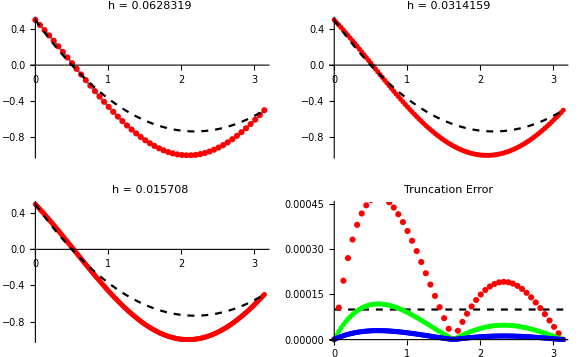

```mathematica
p4=Show[{Plot[y[x]=10^-4,{x,0,Pi},PlotStyle->{Dashed,Black}]},{perr1},{perr2},{perr3},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,Pi},{0,0.00045}}];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```